# Halo flux perturbations

```mathematica
Exit[]
```

```mathematica
path=SetDirectory[NotebookDirectory[]];
SetDirectory[path];
```

```mathematica
<<particlehalo`
```

The notebooks provides the basic procedure to compute the axial/polar GW fluxes at infinity, as a function of the Halo parameters (M,a_0/M) and of the secondary orbital radius. 
Axial perturbations are computed by using either the shooting or the Green function approach. For the polar sector we only use the shooting procedure.

## Axial sector

```mathematica
rparticle=79456 10^-4;(* --- orbital radius of the secondary --- *)
x0=-1/1000-1/100I;
nprec=30;(* --- accuracy of the calculation --- *)
```

```mathematica
rinfinity =1000;(* --- extraction radius at spatial infinity --- *)
deltaσ=1/10;(* --- width of the Gaussian which approximates the Dirac Delta --- *)
```

```mathematica
(* --- Integrator using the shooting approach --- *)
```

```mathematica
masshalo=10;(* --- M --- *)
radiushalo=10;(* --- Subscript[a, 0]/M --- *)
```

The FindRoot search for the  amplitude at the horizon which matches with the correct solution at ∞ that behaves as an outgoing wave

We first find a low-accuracy amplitude using MachinePrecision accuracy. Then we use the amplitude as an initial guess for an high precision FindRoot

### (ℓ,𝓂) = (2,1) - [M=10, a_0 = 10M]

```mathematica
shoot[x0_?NumberQ,σ_,rp_]:=waveaxial[x0,rp,σ,2,1,rinfinity,masshalo,radiushalo,MachinePrecision][[1]]
```

```mathematica
amp=FindRoot[shoot[x,deltaσ,rparticle],{x,x0}][[1,2]]
```

-0.0000519544+0.000109107 ⅈ

```mathematica
waveaxial[amp,rparticle,deltaσ,2,1,rinfinity,masshalo,radiushalo,MachinePrecision]
```

{1.90623×10^-11-9.5003×10^-13 ⅈ,6.89159×10^-7}

```mathematica
x1=SetPrecision[amp,nprec+3];
```

```mathematica
shoot[x0_?NumberQ,σ_,rp_]:=waveaxial[x0,rp,σ,2,1,rinfinity,masshalo,radiushalo,nprec][[1]]
```

```mathematica
Monitor[FindRoot[shoot[x,1/10,rparticle],{x,x1},WorkingPrecision->nprec+3][[1,2]],x];
waveaxial[%,rparticle,1/10,2,1,rinfinity,masshalo,radiushalo,nprec]
```

{-6.71×10^-28+8.738×10^-28 ⅈ,6.915280421567866426223545×10^-7}

```mathematica
(* --- Integrator using the Green Function approach --- *)
```

```mathematica
waveaxialH[rparticle,2,1,rinfinity,masshalo,radiushalo,MachinePrecision]
```

{6.91577×10^-7,1.38554×10^-8}

```mathematica
(* --- the Green function method also gives the flux at the horizon as second output --- *)
waveaxialH[rparticle,2,1,rinfinity,masshalo,radiushalo,nprec]
```

{6.915779017122784605580565×10^-7,1.38553319634525493694567×10^-8}

```mathematica
(* --- relative % difference betwen the two methods --- *)
Abs[6.915280421567866426223545029966319472098817554118885`26.560347045653174*^-7/6.915779017122784605580565397403531974537450980035045`25.459351071497284*^-7-1]100
```

0.00720953566740212626269

## Polar sector

### (ℓ,𝓂) = (2,2) - [M=10, a_0 = 10M, c_sr = 0.9]

Here we test the convergence of the polar shooting method in terms of the width of the Gaussian, which is varied within [0.1,0.005]

```mathematica
rparticle=79456 10^-4;(* --- orbital radius of the secondary --- *)
x0=-1/1000-1/100I;
nprec=30;(* --- accuracy of the calculation --- *)

{speedcs,speecsr}={0,9/10};(* --- Subscript[c, st]/Subscript[c, sr]  --- *)
{masshalo,radiushalo}={10,10};(* --- Subscript[Ma, 0]/M  --- *)
```

```mathematica
rinfinity =1000;(* --- extraction radius at spatial infinity --- *)
```

```mathematica
shoot[x0_?NumberQ,σ_,rp_]:=wavepolarF[x0,rp,σ,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,MachinePrecision][[1]]
```

```mathematica
(* --- explore the parameter @ machine precision --- *)
```

```mathematica
amp=FindRoot[shoot[x,1/10,rparticle],{x,x0}]
```

{x→-0.00817604-0.00883497 ⅈ}

```mathematica
wavepolarF[amp[[1,2]],rparticle,1/10,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,MachinePrecision]
```

{-7.50734×10^-14+6.72181×10^-14 ⅈ,0.000163248}

```mathematica
(* --- increase accuracy --- *)
```

```mathematica
shoot[x0_?NumberQ,σ_,rp_]:=wavepolarF[x0,rp,σ,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,nprec][[1]]
```

```mathematica
x1=SetPrecision[amp[[1,2]],nprec+3]
```

-0.0081760358264445220921601276131696-0.00883496562163685501822829593265851 ⅈ

```mathematica
amps005=Monitor[FindRoot[shoot[x,5/100,rparticle],{x,x1},WorkingPrecision->nprec+3][[1,2]],x]
wavepolarF[%,rparticle,5/100,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,nprec][[2]]
```

-0.00816164257341266111562524344907005-0.00881905638565248164452457747297134 ⅈ

0.000162375517021371504706791006

```mathematica
amps001=Monitor[FindRoot[shoot[x,1/100,rparticle],{x,amps005},WorkingPrecision->nprec+3][[1,2]],x]
wavepolarF[%,rparticle,1/100,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,nprec]
```

-0.00815704962135377320378635411799513-0.00881397238030746506739041805792045 ⅈ

{0.+0. ⅈ,0.00016209739978181215163873805}

```mathematica
amps0025=Monitor[FindRoot[shoot[x,25/1000,rparticle],{x,amps001},WorkingPrecision->nprec+3][[1,2]],x]
wavepolarF[%,rparticle,25/1000,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,nprec][[2]]
```

-0.00815805390238669428678912294079883-0.00881508404454300858696055448906155 ⅈ

0.000162158200341107418453942303

```mathematica
Monitor[FindRoot[shoot[x,1/10,rparticle],{x,x1},WorkingPrecision->nprec+3][[1,2]],x]
wavepolarF[%,rparticle,1/10,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,nprec][[2]]
```

-0.00817602784743832663790742731104296-0.00883497882356557809387436899425298 ⅈ

0.0001632474748504548477231163

```mathematica
amps00025=Monitor[FindRoot[shoot[x,25/10000,rparticle],{x,amps001},WorkingPrecision->nprec+3][[1,2]],x]
wavepolarF[%,rparticle,25/10000,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,nprec][[2]]
```

-0.00815687031061593525459970166230566-0.00881377389604179895418201578628528 ⅈ

0.00016208654475271037568037374

```mathematica
amps0005=Monitor[FindRoot[shoot[x,5/1000,rparticle],{x,amps00025},WorkingPrecision->nprec+3][[1,2]],x]
wavepolarF[%,rparticle,5/1000,2,2,rinfinity,masshalo,radiushalo,speedcs,speecsr,nprec][[2]]
```

-0.00815690617215371264429647625115563-0.00881381359223560120408510317042712 ⅈ

0.00016208871570487797274864946

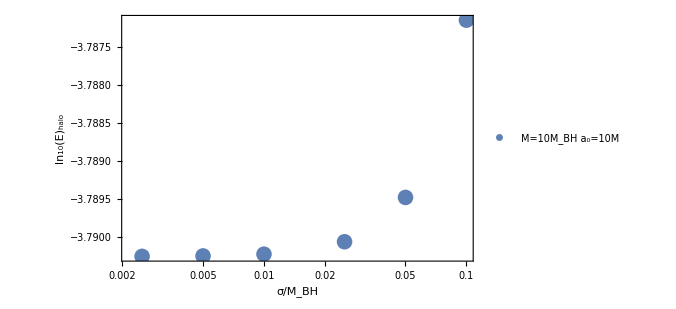

```mathematica
ListLogLinearPlot[{{5/100,Log10[0.0001623755170213715047067910063271520122415335108315963372`27.077363775827223]},{1/100,Log10[0.0001620973997818121516387380511269349933528170392030510174`26.855675457089283]},{25/1000,Log10[0.0001621582003411074184539423025326127843195040270384094803`27.07698709507425]},{1/10,Log10[0.0001632474748504548477231162975297104669297588920114208204`26.831743555482415]},{25/10000,Log10[0.0001620865447527103756803737444897871652946371833425237928`26.849540255157237]},{5/1000,Log10[0.0001620887157048779727486494632965696790364678367440799416`26.850961133098874]}},Frame->True,FrameStyle->Directive[15,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.5]],FrameLabel->{{Style["ln_10(Ė)_halo",20],None},{Style["σ/M_BH",24],None}},ImagePadding->{{100,50},{65,15}},ImageSize->500,Axes->False,PlotRange->All,PlotLegends->Placed[{Style["M=10M_BH a_0=10M",13,FontFamily->"Palatino"]},Scaled[{0.2,0.9}]],PlotMarkers->{{"●",16}}]
```